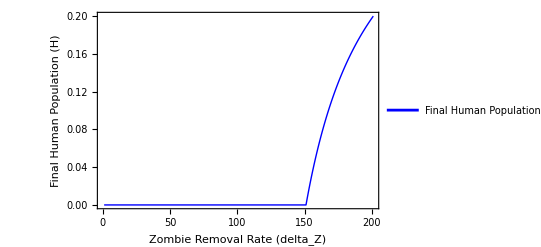

```mathematica
(* Generate the plot of final human population (H) vs. deltaZ *)

finalHValues = Table[
  Module[
    {sol, Hfunc, finalH},
    (* Define the differential equations *)
    eqns = {
      H'[t] == - H[t] Z[t],
      Z'[t] == H[t] Z[t] - δZ H[t] Z[t],
      R'[t] == δZ H[t] Z[t]
    };
    
    (* Solve the system numerically for the current deltaZ *)
    sol = NDSolve[
      {eqns, 
       H[0] == 200/500, 
       Z[0] == 100/500,
       R[0] == 0/500
      },
      {H, Z, R}, 
      {t, 0, 1000000}
    ];
    
    (* Extract the function for H *)
    Hfunc = H /. sol[[1]];
    
    (* Extract the final value of H at time tmax *)
    finalH = Hfunc[1000000];
    
    (* Return the final human value for plotting *)
    finalH
  ],
  {δZ, 0, 2, 0.01} (* Vary deltaZ from 0 to 1 in steps of 0.01 *)
];

(* Plot final human population as a function of deltaZ *)
ListLinePlot[finalHValues, 
 PlotRange -> All,
 PlotLegends -> {"Final Human Population (H) vs. deltaZ"}, 
 PlotStyle -> {Blue, Thick},
 AxesLabel -> {"Zombie Removal Rate (delta_Z)", "Final Human Population (H)"},
 Frame -> True,
 FrameLabel -> {"Zombie Removal Rate (delta_Z)", "Final Human Population (H)"}
]
```